```mathematica
Integrate[-Log[1-t x]/t,{t,0,1}]
```

PolyLog[2,x]

```mathematica
f2[r_]:=(PolyLog[2,2/r]-Log[1-2/r]Log[r/2])(r^2(2r-3))/8+(1+3r-6 r^2)/12 Log[r/2]+11/72+1/(3r)+r/2-r^2/2
```

```mathematica
(*f2[r_]:=1/72 (-49+6 π^2)*)
```

```mathematica
lmt=Limit[f2[r],r->2]
N[lmt]
```

1/72 (-49+6 π^2)

0.141911

```mathematica
substxy2rth={r->Sqrt[x^2+y^2],th->ArcTan[x,y]}
```

{r→√(x^2+y^2),th→ArcTan[x,y]}

```mathematica
Psi2/.substxy2rth/.a->0./.{x->1,y->1.}
```

Psi2

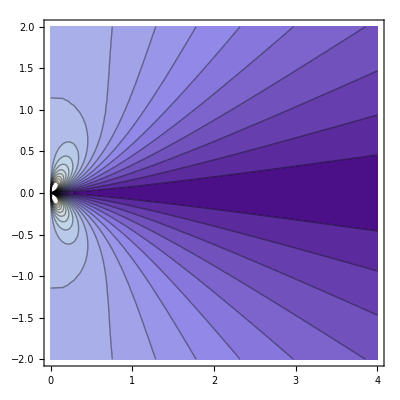

```mathematica
rh:=1+Sqrt[1-a^2]
OmH:=a/(2rh)
Psi0:=1-Cos[th]
Psi2:=Cos[th] Sin[th]^2
Psi:=Psi0+16*OmH^2 f2[r]Psi2
PsiFake:=Psi0+fac2 Psi2
ContourPlot[Sqrt[Psi]/.substxy2rth/.{a->1},{x,0,4},{y,-2,2},Contours->20]
```

```mathematica
Psi//.{r->rh,a->0.9}
```

1-Cos[th]+(0.0197183-7.20662×10^-19 ⅈ) Cos[th] Sin[th]^2

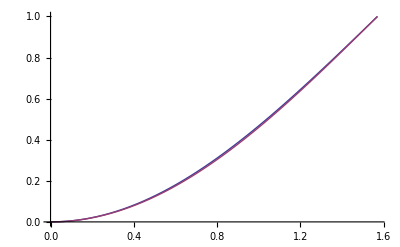

```mathematica
Plot[{(Psi//.{r->rh,a->0.9}),(Psi0//.{r->rh,a->0.999})},{th,0,Pi/2}]
```

```mathematica
rh
```

1+√(1-a^2)

```mathematica
Sig:=r^2+a^2 Cos[th]^2;
gdet:=Sig Sin[th];
Bur=1/gdet D[Psi,th]/.{r->rh}
```

(Csc[th] (Sin[th]+1/(2 (1+√(1-a^2))^2)a^2 Cos[th]^2 (11/72+1/(3 (1+√(1-a^2)))+1/2 (1+√(1-a^2))-1/2 (1+√(1-a^2))^2+1/12 (1+3 (1+√(1-a^2))-6 (1+√(1-a^2))^2) Log[1/2 (1+√(1-a^2))]+1/8 (1+√(1-a^2))^2 (-3+2 (1+√(1-a^2))) (-Log[1/2 (1+√(1-a^2))] Log[1-2/(1+√(1-a^2))]+PolyLog[2,2/(1+√(1-a^2))])) Sin[th]-1/(4 (1+√(1-a^2))^2)a^2 (11/72+1/(3 (1+√(1-a^2)))+1/2 (1+√(1-a^2))-1/2 (1+√(1-a^2))^2+1/12 (1+3 (1+√(1-a^2))-6 (1+√(1-a^2))^2) Log[1/2 (1+√(1-a^2))]+1/8 (1+√(1-a^2))^2 (-3+2 (1+√(1-a^2))) (-Log[1/2 (1+√(1-a^2))] Log[1-2/(1+√(1-a^2))]+PolyLog[2,2/(1+√(1-a^2))])) Sin[th]^3))/((1+√(1-a^2))^2+a^2 Cos[th]^2)

```mathematica
Bur
```

(Csc[th] (Sin[th]+1/(2 (1+√(1-a^2))^2)a^2 Cos[th]^2 (11/72+1/(3 (1+√(1-a^2)))+1/2 (1+√(1-a^2))-1/2 (1+√(1-a^2))^2+1/12 (1+3 (1+√(1-a^2))-6 (1+√(1-a^2))^2) Log[1/2 (1+√(1-a^2))]+1/8 (1+√(1-a^2))^2 (-3+2 (1+√(1-a^2))) (-Log[1/2 (1+√(1-a^2))] Log[1-2/(1+√(1-a^2))]+PolyLog[2,2/(1+√(1-a^2))])) Sin[th]-1/(4 (1+√(1-a^2))^2)a^2 (11/72+1/(3 (1+√(1-a^2)))+1/2 (1+√(1-a^2))-1/2 (1+√(1-a^2))^2+1/12 (1+3 (1+√(1-a^2))-6 (1+√(1-a^2))^2) Log[1/2 (1+√(1-a^2))]+1/8 (1+√(1-a^2))^2 (-3+2 (1+√(1-a^2))) (-Log[1/2 (1+√(1-a^2))] Log[1-2/(1+√(1-a^2))]+PolyLog[2,2/(1+√(1-a^2))])) Sin[th]^3))/((1+√(1-a^2))^2+a^2 Cos[th]^2)

```mathematica
FullSimplify[Bur/.{a->0.,fac2->0}]
```

Indeterminate

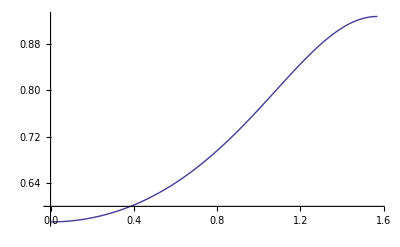

```mathematica
Plot[(Bur/.{a->1,fac2->0.0}),{th,0,Pi/2}]
```

```mathematica
PsiFake
```

1-Cos[th]+fac2 Cos[th] Sin[th]^2